## Perform AUC calculations for a normal distribution

```mathematica
fx[x_]:=1/(√(2π))Exp[-1/2(x)^2];
fnormal[x_,mu_,sigma_]:=1/sigma*fx[(x-mu)/sigma];
```

### Create export function

```mathematica
plotexporter[plotObject_,path_]:=Export[path,plotObject];
```

### Create average calculator

```mathematica
average[data_]:=1/Length[data]*Sum[data[[i]],{i,1,Length[data]}];
```

### Create the normal distribution based on the normal function “fnormal”

```mathematica
normalTuple[x_,mu_,sigma_]:={x,fnormal[x,mu,sigma]};
distribution[mu_,sigma_,delta_]:=Table[normalTuple[arg,mu,sigma],{arg,-delta,delta,0.1}];
fdist[mu_,sigma_,delta_]:=Table[fnormal[arg,mu,sigma],{arg,-delta,delta,0.1}];
```

### Calculate the average delta between the x-arguments

```mathematica
dx[params_]:=Table[distribution[params[[1]],params[[2]],params[[3]]][[n]][[2]]-distribution[params[[1]],params[[2]],params[[3]]][[n-1]][[2]],{n,2,Length[distribution[params[[1]],params[[2]],params[[3]]]]}];
avgdx[params_]:=Mean[dx[params[[1]],params[[2]],params[[3]]]];
```

### Create a graphical representation of the normal distribution Set a group of testing parameters: mean μ, standard deviation σ, the “spread” of the distribution δ

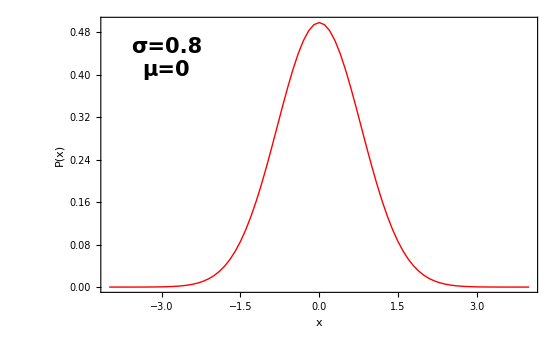

```mathematica
testParams={0,0.8,4};
distPlotter[params_]:=ListPlot[distribution[params[[1]],params[[2]],params[[3]]],Joined->True,PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"x","P(x)"},FrameStyle->Directive[Black,Thick],ImageSize->{560.,420.},Epilog->Inset[Style[StringTemplate["σ=``\nμ=``"][params[[2]],params[[1]]],Bold,Black,21,FontFamily->"Times"],Scaled[{0.15,0.85}]]];
Show[distPlotter[testParams]]
```

```mathematica
aucLeft[params_,rightLimit_]:=1;
```

{1.58653×10^-6,2.84196×10^-6,5.0086×10^-6,8.68419×10^-6,0.0000148129,0.0000248558,0.0000410273,0.0000666122,0.000106377,0.00016708,0.000258082,0.000392026,0.000585545,0.000859911,0.00124151,0.00176199,0.00245784,0.0033693,0.00453827,0.00600515,0.0078045,0.00995969,0.0124767,0.0153375,0.0184941,0.0218638,0.0253262,0.0287242,0.0318683,0.034546,0.0365345,0.0376176,0.0376053,0.036353,0.0337794,0.0298804,0.0247372,0.0185163,0.011462,0.00388074,-0.00388074,-0.011462,-0.0185163,-0.0247372,-0.0298804,-0.0337794,-0.036353,-0.0376053,-0.0376176,-0.0365345,-0.034546,-0.0318683,-0.0287242,-0.0253262,-0.0218638,-0.0184941,-0.0153375,-0.0124767,-0.00995969,-0.0078045,-0.00600515,-0.00453827,-0.0033693,-0.00245784,-0.00176199,-0.00124151,-0.000859911,-0.000585545,-0.000392026,-0.000258082,-0.00016708,-0.000106377,-0.0000666122,-0.0000410273,-0.0000248558,-0.0000148129,-8.68419×10^-6,-5.0086×10^-6,-2.84196×10^-6,-1.58653×10^-6}

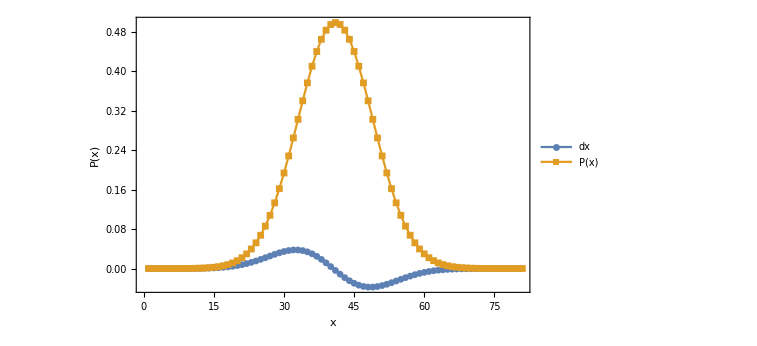

μ_dx=0.000000000000000000561453

```mathematica
dx[testParams[[1]],testParams[[2]],testParams[[3]]]
ListPlot[{dx[testParams[[1]],testParams[[2]],testParams[[3]]],fdist[testParams[[1]],testParams[[2]],testParams[[3]]]},PlotRange->Full,ImageSize->{560.,420.},Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[{dx,"P(x)"},{0.2,0.8}],FrameLabel->{"x","P(x)"},LabelStyle->{18,Bold,Black,FontFamily->"Times"}]
Print[Style[StringTemplate["μ_dx=``"][avgdx[testParams]],20,Red,Bold,FontFamily->"Times"]]
```